This notebook checks the derivation of Lemma 2.5.
For non-integers, the binomial function is replaced by Gamma functions.

```mathematica
GeneralBinomial[m_, n_]:= Gamma[m+1]/Gamma[n+1] / Gamma[m-n+1];
```

For odd indexed terms, the summation can be converted to hypergeometric function of type 1F2.

```mathematica
B[m_, q_, σ_]:=(-1)^m /2 * Sum[ (GeneralBinomial[l/2 - 1, q+m] * GeneralBinomial[l/2, q] + GeneralBinomial[l/2 , q+m] * GeneralBinomial[l/2 - 1, q] )* (-σ)^l/Gamma[l+1], {l, 1, Infinity, 2}];
```

```mathematica
B2[m_, q_, σ_]:= -(-1)^m / 2 * σ*(GeneralBinomial[-1/2, m+q]*GeneralBinomial[1/2, q]*HypergeometricPFQ[{1/2}, {3/2-q, 1/2-m-q}, σ^2/4] + GeneralBinomial[1/2, m+q]*GeneralBinomial[-1/2, q]*HypergeometricPFQ[{1/2}, {1/2-q, 3/2-m-q}, σ^2/4])
```

```mathematica
(* Test if B and B2 are equal. *)
```

```mathematica
N[Table[B[6, q, 4], {q, 0, 10}]] - N[Table[B2[6, q, 4], {q, 0, 10}]]
```

{5.38458×10^-15,-1.38778×10^-17,1.38778×10^-17,1.38778×10^-17,-1.04083×10^-17,-7.11237×10^-17,0.,0.,0.,0.,0.}

For even indexed terms, the summation also generates hypergeometric function but the summation form is easier to perform analysis.

```mathematica
A[m_, q_, σ_]:= (-1)^m / 2*Sum[(GeneralBinomial[l/2 - 1, q+m] * GeneralBinomial[l/2, q] + GeneralBinomial[l/2 , q+m] * GeneralBinomial[l/2-1, q])* (-σ)^l/Gamma[l+1], {l, 2, Infinity, 2}];
```

```mathematica
A2[m_, q_, σ_]:= (-1)^m /4 * σ^2 * (Sum[Binomial[n, q]*Binomial[n+1, m+q]*σ^(2n)/Factorial[2n+1]/(n+1), {n, 0, Infinity}] + Sum[Binomial[n+1, q]*Binomial[n, m+q]*σ^(2n)/Factorial[2n+1]/(n+1), {n, 0, Infinity}])
```

```mathematica
(* Verify A2 and A are identical *)
```

```mathematica
N[Table[A[6, q, 4], {q, 0, 10}]] - N[Table[A2[6, q, 4], {q, 0, 10}]]
```

{-5.86337×10^-15,3.46945×10^-18,8.67362×10^-19,-3.25261×10^-19,4.06576×10^-20,-8.47033×10^-22,0.,1.65436×10^-24,0.,-2.42338×10^-26,-7.06819×10^-28}

The first term is special, we deal with it separately.

```mathematica
R[m_, q_] := ((-1)^(m+q) * KroneckerDelta[q, 0] + (-1)^q * KroneckerDelta[m+q, 0])/2;
```

```mathematica
c[m_, q_, σ_] :=R[m, q] + A2[m, q, σ] + B2[m, q, σ]
```

Mathematica will perform some simplification by itself. The following form is not friendly for numerical evaluation.

```mathematica
c[m, q, σ]
```

-1/2 (-1)^m σ ((π HypergeometricPFQ[{1/2},{1/2-q,3/2-m-q},σ^2/4])/(2 Gamma[1/2-q] Gamma[3/2-m-q] Gamma[1+q] Gamma[1+m+q])+(π HypergeometricPFQ[{1/2},{3/2-q,1/2-m-q},σ^2/4])/(2 Gamma[3/2-q] Gamma[1/2-m-q] Gamma[1+q] Gamma[1+m+q]))+1/4 (-1)^m σ^2 (Binomial[0,q] Binomial[1,m+q] HypergeometricPFQ[{1,1},{3/2,1-q,2-m-q},σ^2/4]+Binomial[0,m+q] Binomial[1,q] HypergeometricPFQ[{1,1},{3/2,2-q,1-m-q},σ^2/4])+1/2 ((-1)^(m+q) 0,q+(-1)^q 0,m+q)

```mathematica
(* Mathematica simplifies but can only evaluate using limit *)
```

For comparison, we also test the simplified version. It will be faster but needs to use small offsets.

```mathematica
simpCoeff[m_, q_,σ_]:= -1/2 (-1)^m σ ((π HypergeometricPFQ[{1/2},{1/2-q,3/2-m-q},σ^2/4])/(2 Gamma[1/2-q] Gamma[3/2-m-q] Gamma[1+q] Gamma[1+m+q])+(π HypergeometricPFQ[{1/2},{3/2-q,1/2-m-q},σ^2/4])/(2 Gamma[3/2-q] Gamma[1/2-m-q] Gamma[1+q] Gamma[1+m+q]))+1/4 (-1)^m σ^2 (Binomial[0,q] Binomial[1,m+q] HypergeometricPFQ[{1,1},{3/2,1-q,2-m-q},σ^2/4]+Binomial[0,m+q] Binomial[1,q] HypergeometricPFQ[{1,1},{3/2,2-q,1-m-q},σ^2/4])
```

```mathematica
(* Fast evaluation if we take non-integer values *)
```

```mathematica
FastCoeff[m_, q_, σ_]:=Re[( N[simpCoeff[m+10^-25, q+10^-25, σ], 90] +1/2 ((-1)^(m+q) 0,q+(-1)^q 0,m+q))]
```

```mathematica
Coeff[m_, q_, σ_]:=(-1)^m /2 *Sum[(Binomial[l/2 - 1, q+m]*Binomial[l/2, q] + Binomial[l/2 , q+m]*Binomial[l/2-1, q] ) * (-σ)^l/Factorial[l], {l, 0, Infinity}]
```

```mathematica
(* Verify the derivation is correct *)
```

```mathematica
N[Table[c[6, q, 4],{q, 0, 5}]]
```

{0.153481,0.135226,0.0706826,0.035502,0.0207522,0.0139317}

```mathematica
N[Table[Coeff[6, q, 4],{q, 0, 5}]]
```

{0.153481,0.135226,0.0706826,0.035502,0.0207522,0.0139317}

```mathematica
(* check the asymptotic of c_{m, 0} *)
```

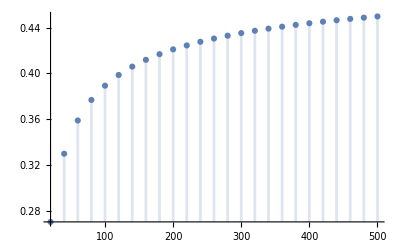

```mathematica
DiscretePlot[c[m, 0, 4], {m, 20, 500, 20}]
```

```mathematica
Sum[FastCoeff[6, q, 4], {q, 0, 500}]
```

0.510937486802594207515086968001605096723849146138880289782909798403732399201589159192433928

```mathematica
(* Sum of coefficients *)
```

```mathematica
sumCoeff[m_, σ_] := 1/2 + NIntegrate[Exp[-2*σ * Sin[t/2]] * Cos[m * t], {t, 0, 2Pi}]/(4Pi)
```

```mathematica
sumCoeff[6, 4]
```

0.512202